# 2D First-Passage

## Drift towards the equilibrium at (x~, y~) = (0, 0) with an absorbing boundary at x~=x~*.

## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP=λt*D[yt*P[xt, yt], xt]+D[yt*P[xt, yt], yt]-κt*D[xt*P[xt, yt],yt]+(1/2)D[P[xt, yt],{xt,2}]+(1/2)D[P[xt, yt],{yt,2}];
```

## Get the steady-state variances

```mathematica
A= {{ 0,λt},{-κt, 1}}
B = {{1,0},{0,1}}
s=Array[Y,{2,2}]
ss =( s/. Expand[FullSimplify[Solve[A.s+s.Transpose[A]==B.Transpose[B], Flatten[s]]]])[[1]]
```

{{0,λt},{-κt,1}}

{{1,0},{0,1}}

{{Y[1,1],Y[1,2]},{Y[2,1],Y[2,2]}}

{{1/2+1/(2 κt λt)+λt/(2 κt),1/(2 λt)},{1/(2 λt),1/2+κt/(2 λt)}}

## Choose the parameter values

```mathematica
λts = {0.05, 0.1, 0.2, 0.5,0.8};
κts = {0.3, 0.5, 0.8, 1.0, 1.2};
κScale =N[ Flatten[Table[κts^2/2, 5]] ];(*For scaling the flux to a probability distribtion*)
params = Flatten[Table[{λt->l, κt->k}, {l, λts}, {k, κts}], 1]
legend =  Flatten[Table["λt="<>ToString[l]<>"; "<> "κt="<>ToString[k], {l, λts},{k, κts}], 1];
```

{{λt→0.05,κt→0.3},{λt→0.05,κt→0.5},{λt→0.05,κt→0.8},{λt→0.05,κt→1.},{λt→0.05,κt→1.2},{λt→0.1,κt→0.3},{λt→0.1,κt→0.5},{λt→0.1,κt→0.8},{λt→0.1,κt→1.},{λt→0.1,κt→1.2},{λt→0.2,κt→0.3},{λt→0.2,κt→0.5},{λt→0.2,κt→0.8},{λt→0.2,κt→1.},{λt→0.2,κt→1.2},{λt→0.5,κt→0.3},{λt→0.5,κt→0.5},{λt→0.5,κt→0.8},{λt→0.5,κt→1.},{λt→0.5,κt→1.2},{λt→0.8,κt→0.3},{λt→0.8,κt→0.5},{λt→0.8,κt→0.8},{λt→0.8,κt→1.},{λt→0.8,κt→1.2}}

## Get the trajectory of the mean

```mathematica
eig=FullSimplify[Eigenvectors[A]]
```

{{(1+√(1-4 κt λt))/(2 κt),1},{-(-1+√(1-4 κt λt))/(2 κt),1}}

```mathematica
Eigenvalues[A]
```

{1/2 (1-√(1-4 κt λt)),1/2 (1+√(1-4 κt λt))}

```mathematica
cstar =Re[N[ Flatten[Table[(eig[[1,1]])^-1/.p, {p, params}]]]]
```

{0.30464,0.513167,0.834849,1.05573,1.2822,0.309584,0.527864,0.876894,1.12702,1.39445,0.320551,0.563508,1.,1.38197,2.,0.367544,1.,1.,1.,1.,0.5,0.625,0.625,0.625,0.625}

## Set up the mesh, boundary conditions, and initial condition

#### Steady-state distribution widths in x~, y~

```mathematica
xtwidths = N[Table[ss[[1,1]]/.p, {p, params}]];
ytwidths = N[Table[ss[[2,2]]/.p, {p, params}]];
xtStds =Sqrt[xtwidths]
ytStds = Sqrt[ytwidths]
```

{5.8238,4.53321,3.60988,3.24423,2.9756,4.16333,3.25576,2.61008,2.35584,2.16987,3.02765,2.38747,1.93649,1.76068,1.63299,2.16025,1.73205,1.43614,1.32288,1.24164,1.97906,1.59687,1.33463,1.23491,1.16369}

{1.87083,2.34521,2.91548,3.24037,3.53553,1.41421,1.73205,2.12132,2.34521,2.54951,1.11803,1.32288,1.58114,1.73205,1.87083,0.894427,1.,1.14018,1.22474,1.30384,0.829156,0.901388,1.,1.06066,1.11803}

```mathematica
deltaWidth = 0.05;
deltaVar = deltaWidth^2;
minCell = deltaWidth/5;
```

#### Boundary condition at x~* -> y~* = c~ x~*. Choose the boundaries to be far enough away from the initial condition and the final distribution

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
xt0 = 25;
xtls=-5*xtStds
xtrs = xt0+5*xtStds
ytls=cstar
ytrs = cstar*xt0+5*ytStds
```

{-29.119,-22.6661,-18.0494,-16.2211,-14.878,-20.8167,-16.2788,-13.0504,-11.7792,-10.8493,-15.1383,-11.9373,-9.68246,-8.80341,-8.16497,-10.8012,-8.66025,-7.1807,-6.61438,-6.20819,-9.89529,-7.98436,-6.67317,-6.17454,-5.81843}

{54.119,47.6661,43.0494,41.2211,39.878,45.8167,41.2788,38.0504,36.7792,35.8493,40.1383,36.9373,34.6825,33.8034,33.165,35.8012,33.6603,32.1807,31.6144,31.2082,34.8953,32.9844,31.6732,31.1745,30.8184}

{0.30464,0.513167,0.834849,1.05573,1.2822,0.309584,0.527864,0.876894,1.12702,1.39445,0.320551,0.563508,1.,1.38197,2.,0.367544,1.,1.,1.,1.,0.5,0.625,0.625,0.625,0.625}

{16.9702,24.5552,35.4486,42.5951,49.7327,14.8107,21.8569,32.529,39.9015,47.6088,13.6039,20.7021,32.9057,43.2094,59.3541,13.6607,30.,30.7009,31.1237,31.5192,16.6458,20.1319,20.625,20.9283,21.2152}

```mathematica
icPos =Table[{xt0, c*xt0}, {c, cstar}];
icVar ={{deltaVar, 0},{0, deltaVar}}
ic0 = N[Table[PDF[MultinormalDistribution[pos,icVar], {xt, yt}], {pos, icPos}]];
Sqrt[icVar]
bcFunc[xtl_, xtr_, ytl_, ytr_] :={
	  P[xtl, yt]==0,
           P[xtr, yt]==0,
           P[xt, ytr]==0,
           P[xt, ytl]==0
};
ΩFunc[xtl_, xtr_, ytl_, ytr_] :=ImplicitRegion[True,{{xt,xtl,xtr},{yt,ytl,ytr}}];
bcs = MapThread[bcFunc, {xtls, xtrs, ytls, ytrs}];
cellDistances = Table[minCell, 25]
Ω=MapThread[ΩFunc,{xtls, xtrs, ytls, ytrs}];
```

{{0.0025,0},{0,0.0025}}

{{0.05,0},{0,0.05}}

{0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01}

```mathematica
ytCheckFunc[ytl_, c_]:=c≤ ytl
```

```mathematica
MapThread[ytCheckFunc, {cstar*xt0-5*ytStds, cstar}]
```

{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

General::munfl: 1/2.71828^596332. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^617012. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^670232. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

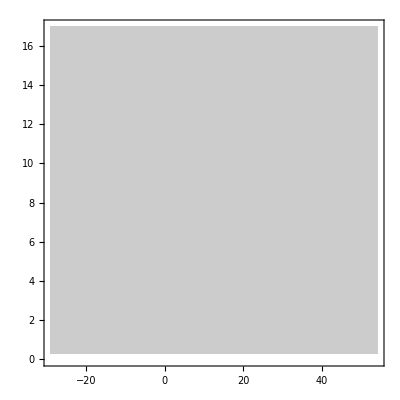

```mathematica
toPlot=1;
ContourPlot[ic0[[toPlot]], {xt, xtls[[toPlot]], xtrs[[toPlot]]}, {yt, ytls[[toPlot]], ytrs[[toPlot]]}, PlotRange->Automatic, PlotLegends->Automatic]
```

## Calculate the time-integrated probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, reg_, cell_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bc],
                                   P,{xt, yt}∈reg, 
Method->{"FiniteElement", "MeshOptions"->{"MaxCellMeasure"->cell}}];
Return[(P/.N[[1]])];
]
```

```mathematica
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, Ω, cellDistances}];
```

```mathematica
solsIc0[[1]]["ElementMesh"]["Wireframe"]
```

-Graphics-

```mathematica
fluxXIc0 = Table[Derivative[0,1][sol],{sol, solsIc0}];
```

General::munfl: 1/2.71828^596332. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^617012. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^670232. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

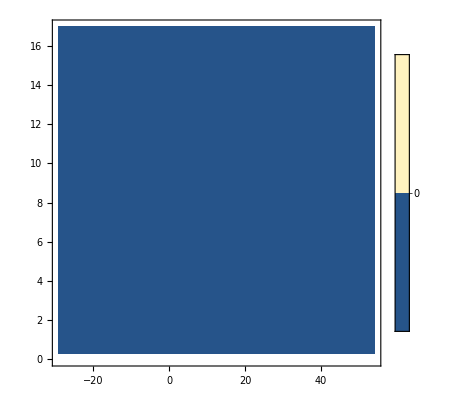

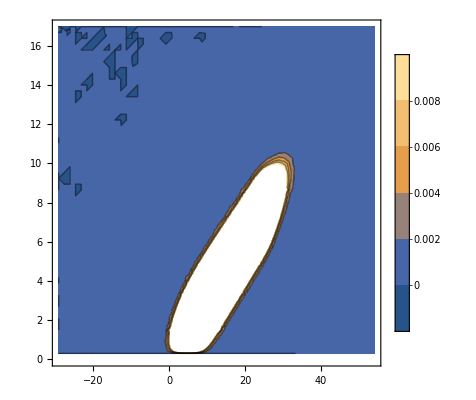

```mathematica
toPlot=1;
ContourPlot[ic0[[toPlot]], {xt, xtls[[toPlot]], xtrs[[toPlot]]}, {yt, ytls[[toPlot]], ytrs[[toPlot]]}, PlotRange->{0, 0.001}, PlotLegends->Automatic]
ContourPlot[solsIc0[[toPlot]][xt, yt], {xt, xtls[[toPlot]], xtrs[[toPlot]]}, {yt, ytls[[toPlot]], ytrs[[toPlot]]}, PlotLegends->Automatic, PlotRange->{-0.001,0.01}]
```

```mathematica
XIc0 =(MapThread[#1[xt,#2]&,{fluxXIc0,ytls}])/2;
```

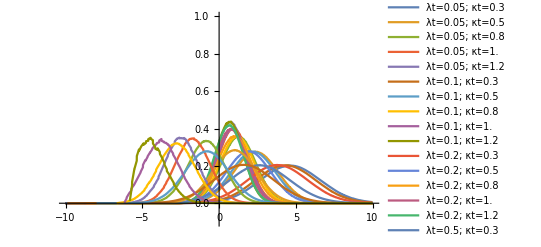

```mathematica
Plot[XIc0, {xt, -10, 10}, PlotRange->{-0.1, 1}, PlotLegends->legend]
```

```mathematica
IntegFunc[f_, l_, r_] := NIntegrate[f, {xt, l, r}, WorkingPrecision->10]
```

```mathematica
normsIc0 = MapThread[IntegFunc, {XIc0, xtls/2, xtrs/2}]
corrected = MapThread[#1/#2&, {XIc0, normsIc0}];
meansIc0= MapThread[IntegFunc, {XIc0*xt, xtls, xtrs}]
secondIc0 = MapThread[IntegFunc, {XIc0*xt*xt, xtls, xtrs}]
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0^2;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {3.972354687}. NIntegrate obtained 1.000497622 and 0.0002718956539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.177141702}. NIntegrate obtained 1.000540177 and 0.0003111031897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {0.4710086484}. NIntegrate obtained 1.0019727 and 0.0002559643752 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{1.000497622,0.9994104067,1.000540177,1.0019727,0.9978148007,0.9998661122,0.9988073256,1.001025651,0.9942765788,0.9984236245,1.000768927,1.002220896,1.000974412,0.9992371713,0.9946616699,1.001767588,1.002586871,0.9820589963,0.9061134941,0.6943630907,1.001726439,0.9834641682,0.6638533426,0.2657212021,0.05588059581}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {7.456986616}. NIntegrate obtained 4.66723901 and 0.001950819531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {4.942079499}. NIntegrate obtained 2.392905091 and 0.0008494228638 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.638281575}. NIntegrate obtained 1.267329957 and 0.0003203836461 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{4.66723901,2.392905091,1.267329957,0.9342251579,0.7245827905,4.355603398,2.222761877,1.174690982,0.8629246871,0.6866902157,3.841272321,1.92554522,1.002771737,0.7543746074,0.6456644724,2.685888379,1.018418723,-0.8274408249,-1.682594563,-2.357887945,1.633635526,-0.7908877912,-2.691940388,-3.462530547,-3.219005718}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {8.269857879}. NIntegrate obtained 25.7228778 and 0.01128763478 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {4.942079499}. NIntegrate obtained 7.836428499 and 0.003916084775 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {3.308952508}. NIntegrate obtained 2.852789291 and 0.001221037326 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{25.7228778,7.836428499,2.852789291,1.868939122,1.361305029,22.84781721,7.032694323,2.627511104,1.740452439,1.310359336,18.58156432,5.776949199,2.251810621,1.579528437,1.323851968,11.09585349,3.026257441,2.08323824,4.144909667,6.94121103,6.446583308,2.668284131,8.868811816,13.793463,14.28603364}

{3.9397578,2.11043373,1.24666407,0.996162476,0.836284809,3.8765362,2.09202396,1.2476122,0.995813423,0.838815883,3.8261913,2.0692248,1.24625946,1.01044739,0.906969357,3.88185711,1.98908075,1.39857992,1.3137852,1.3815755,3.77781828,2.04278063,1.6222688,1.8043452,3.92403583}

```mathematica
grid = Flatten[Table[{l, s}, {l, λts}, {s, κts}], 1];
params
```

{{λt→0.05,κt→0.3},{λt→0.05,κt→0.5},{λt→0.05,κt→0.8},{λt→0.05,κt→1.},{λt→0.05,κt→1.2},{λt→0.1,κt→0.3},{λt→0.1,κt→0.5},{λt→0.1,κt→0.8},{λt→0.1,κt→1.},{λt→0.1,κt→1.2},{λt→0.2,κt→0.3},{λt→0.2,κt→0.5},{λt→0.2,κt→0.8},{λt→0.2,κt→1.},{λt→0.2,κt→1.2},{λt→0.5,κt→0.3},{λt→0.5,κt→0.5},{λt→0.5,κt→0.8},{λt→0.5,κt→1.},{λt→0.5,κt→1.2},{λt→0.8,κt→0.3},{λt→0.8,κt→0.5},{λt→0.8,κt→0.8},{λt→0.8,κt→1.},{λt→0.8,κt→1.2}}

```mathematica
normArrayIc0 = ArrayReshape[normsIc0, {5,5}];
varArrayIc0 = ArrayReshape[varsIc0, {5,5}];
meanArrayIc0 = ArrayReshape[meansIc0, {5,5}];
diffArrayIc0 = ArrayReshape[diffIc0,{5,5}];
```

```mathematica
cf[x_]:=Blend[{{0, Red},{ 1,White},{5,Blue}}, x]
xticks = Transpose[{{1, 2, 3, 4, 5}, λts}];
yticks = Transpose[{{1, 2, 3, 4, 5}, κts}];
```

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var("OverTilde[xt]   .")"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]
Grid[N[Reverse[varArrayIc0],4]]
Grid[N[Reverse[normArrayIc0],4]]

ArrayPlot[ArrayReshape[Table[Blend[{{0, Red},{ 1,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {5,5}], PlotLegends->{Placed[BarLegend[{cf[#]&,{0, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]
Grid[N[Reverse[meanArrayIc0],4]]

ArrayPlot[diffArrayIc0, ColorFunction->(Blend[{{ 0,White},{3,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"varScaledToMean2(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]
Grid[N[Reverse[diffArrayIc0],4]]
```

-Graphics-

3.778 | 2.043 | 1.622 | 1.804 | 3.924
3.882 | 1.989 | 1.399 | 1.314 | 1.382
3.826 | 2.069 | 1.246 | 1.01 | 0.907
3.877 | 2.092 | 1.248 | 0.9958 | 0.8388
3.94 | 2.11 | 1.247 | 0.9962 | 0.8363

1.002 | 0.9835 | 0.6639 | 0.2657 | 0.05588
1.002 | 1.003 | 0.9821 | 0.9061 | 0.6944
1.001 | 1.002 | 1.001 | 0.9992 | 0.9947
0.9999 | 0.9988 | 1.001 | 0.9943 | 0.9984
1. | 0.9994 | 1.001 | 1.002 | 0.9978

-Graphics-

1.634 | -0.7909 | -2.692 | -3.463 | -3.219
2.686 | 1.018 | -0.8274 | -1.683 | -2.358
3.841 | 1.926 | 1.003 | 0.7544 | 0.6457
4.356 | 2.223 | 1.175 | 0.8629 | 0.6867
4.667 | 2.393 | 1.267 | 0.9342 | 0.7246

-Graphics-

1.416 | 3.266 | 0.2239 | 0.1505 | 0.3787
0.5381 | 1.918 | 2.043 | 0.4641 | 0.2485
0.2593 | 0.5581 | 1.239 | 1.776 | 2.176
0.2043 | 0.4234 | 0.9041 | 1.337 | 1.779
0.1809 | 0.3686 | 0.7762 | 1.141 | 1.593

```mathematica
VarX =Table[ss[[1,1]]/.p, {p, params}];
VarXArray = ArrayReshape[VarX, {5, 5}];
ArrayPlot[VarXArray, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var("OverTilde[xt]   .")"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]
Grid[N[Reverse[VarXArray],4]]
```

-Graphics-

3.91667 | 2.55 | 1.78125 | 1.525 | 1.35417
4.66667 | 3. | 2.0625 | 1.75 | 1.54167
9.16667 | 5.7 | 3.75 | 3.1 | 2.66667
17.3333 | 10.6 | 6.8125 | 5.55 | 4.70833
33.9167 | 20.55 | 13.0313 | 10.525 | 8.85417

```mathematica
VarY =Table[ss[[2,2]]/.p, {p, params}];
VarYArray = ArrayReshape[VarY, {5, 5}];
ArrayPlot[VarYArray, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var("OverTilde[yt]   .")"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]
Grid[N[Reverse[VarYArray],4]]
```

-Graphics-

0.6875 | 0.8125 | 1. | 1.125 | 1.25
0.8 | 1. | 1.3 | 1.5 | 1.7
1.25 | 1.75 | 2.5 | 3. | 3.5
2. | 3. | 4.5 | 5.5 | 6.5
3.5 | 5.5 | 8.5 | 10.5 | 12.5

#### Check that all s.s. variances have been reached before mean passage

```mathematica
S[A_, B_] := FullSimplify[Integrate[MatrixExp[-A*(t-tp)].B.Transpose[B].MatrixExp[-Transpose[A]*(t-tp)], {tp, 0, t}]];
```

```mathematica
As = {{ 0,λ},{-κ, 1}}
Bs = {{1,0},{0,κ }}
s0[λ_, κ_, t_] = FullSimplify[MatrixExp[-{{ 0,λ},{-κ, 1}}*t].icVar.MatrixExp[-Transpose[{{ 0,λ},{-κ, 1}}]*t]];
```

{{0,λ},{-κ,1}}

{{1,0},{0,κ}}

{{1/(-0.25+1. κ λ)(ⅇ^-t λ (-2.5+12.755 κ+1.17563 λ)+ⅇ^(-t (1+√(1-4 κ λ))) (-3.18875+3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ-1.25 √(1-4 κ λ)))+ⅇ^(t (-1+√(1-4 κ λ))) (-3.18875-3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ+1.25 √(1-4 κ λ)))),1/(-0.25+1. κ λ)(-3.18875 Cosh[t]+3.18875 Sinh[t]) (0.392003-2. κ-0.184339 λ+(κ (2.-1.56801 λ)+0.184339 λ) Cosh[t √(1-4 κ λ)]+2. (1. κ-0.0921697 λ) √(1-4 κ λ) Sinh[t √(1-4 κ λ)])},{1/(-0.25+1. κ λ)(-3.18875 Cosh[t]+3.18875 Sinh[t]) (0.392003-2. κ-0.184339 λ+(κ (2.-1.56801 λ)+0.184339 λ) Cosh[t √(1-4 κ λ)]+2. (1. κ-0.0921697 λ) √(1-4 κ λ) Sinh[t √(1-4 κ λ)]),1/(-0.25+1. κ λ)(ⅇ^-t κ (-2.5+12.755 κ+1.17563 λ)+ⅇ^(t (-1+√(1-4 κ λ))) (-0.293906+0.293906 √(1-4 κ λ)+κ (1.25-6.3775 κ+0.587813 λ-1.25 √(1-4 κ λ)))+ⅇ^(-t (1+√(1-4 κ λ))) (-0.293906-0.293906 √(1-4 κ λ)+κ (1.25-6.3775 κ+0.587813 λ+1.25 √(1-4 κ λ))))}}

```mathematica
S0 =%532[[1,1]];
```

1/(-0.25+1. κ λ)(ⅇ^-t λ (-2.5+12.755 κ+1.17563 λ)+ⅇ^(-t (1+√(1-4 κ λ))) (-3.18875+3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ-1.25 √(1-4 κ λ)))+ⅇ^(t (-1+√(1-4 κ λ))) (-3.18875-3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ+1.25 √(1-4 κ λ))))

```mathematica
curve =S[As, Bs];
```

{{(((1-ⅇ^(-t (1+√(1-4 κ λ)))) (-1+√(1-4 κ λ)-2 κ λ (-1+κ λ)))/(1+√(1-4 κ λ))-((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (1+√(1-4 κ λ)+2 κ λ (-1+κ λ)))/(-1+√(1-4 κ λ))+4 κ λ (1+κ λ) (1-Cosh[t]+Sinh[t]))/(-2+8 κ λ),(ⅇ^(-t (2+√(1-4 κ λ))) (-4 ⅇ^(t (1+√(1-4 κ λ))) κ λ (1+κ λ)+ⅇ^(t (2+√(1-4 κ λ))) (-2+8 κ λ)+ⅇ^t (1-√(1-4 κ λ)+2 κ λ (-1+κ λ))+ⅇ^(t+2 t √(1-4 κ λ)) (1+√(1-4 κ λ)+2 κ λ (-1+κ λ))))/(4 λ (-1+4 κ λ))},{(ⅇ^(-t (2+√(1-4 κ λ))) (-4 ⅇ^(t (1+√(1-4 κ λ))) κ λ (1+κ λ)+ⅇ^(t (2+√(1-4 κ λ))) (-2+8 κ λ)+ⅇ^t (1-√(1-4 κ λ)+2 κ λ (-1+κ λ))+ⅇ^(t+2 t √(1-4 κ λ)) (1+√(1-4 κ λ)+2 κ λ (-1+κ λ))))/(4 λ (-1+4 κ λ)),(κ^2 (-((1-ⅇ^(-t (1+√(1-4 κ λ)))) (3-2 κ λ+√(1-4 κ λ)))/(1+√(1-4 κ λ))+((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (-3+2 κ λ+√(1-4 κ λ)))/(-1+√(1-4 κ λ))+4 (1+κ λ) (1-Cosh[t]+Sinh[t])))/(-2+8 κ λ)}}

```mathematica
toPlotCurve[λ_, κ_, t_]=1.05S0+curve[[1,1]];
```

1/(-0.25+1. κ λ)1.05 (ⅇ^-t λ (-2.5+12.755 κ+1.17563 λ)+ⅇ^(-t (1+√(1-4 κ λ))) (-3.18875+3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ-1.25 √(1-4 κ λ)))+ⅇ^(t (-1+√(1-4 κ λ))) (-3.18875-3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ+1.25 √(1-4 κ λ))))+(((1-ⅇ^(-t (1+√(1-4 κ λ)))) (-1+√(1-4 κ λ)-2 κ λ (-1+κ λ)))/(1+√(1-4 κ λ))-((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (1+√(1-4 κ λ)+2 κ λ (-1+κ λ)))/(-1+√(1-4 κ λ))+4 κ λ (1+κ λ) (1-Cosh[t]+Sinh[t]))/(-2+8 κ λ)

```mathematica
Manipulate[Plot[{toPlotCurve[λ, κ, t], 1/2+1/(2 κ λ)+(κ λ)/2}, {t, 0, 35}, PlotRange->{0, 35}, GridLines->{{{tfPlot [λ, κ, 8],Red}},None}], {λ, 0.01, 0.5}, {κ, 0.2, 0.45}]
```

```mathematica
tfPlot [λ_, κ_, x0_] := (1/λ)*Log[x0/(2*κ/(1+Sqrt[1-4*λ*κ]))]
```